```mathematica
filepathname="/home/thomas/Desktop/distancematrix.txt";
linectr=1;
While[UnsameQ[(line=ReadLine[filepathname]),EndOfFile],distancerow[linectr]=(ToExpression@StringSplit[line," "])/49.7484;If[Mod[linectr,1000]==0,Print[linectr]];linectr++];
n=linectr-1
```

1000

2000

3000

4000

5000

6000

7000

8000

9000

10000

10001

```mathematica
data=Table[distancerow[i],{i,n-1}];
```

```mathematica
MyPlot[data_]:=MatrixPlot[data,PlotRangePadding->0,PlotTheme->"Scientific",LabelStyle->Directive[Black,FontColor->Black,24,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,20,FontFamily->"CMU Serif",Plain],FrameLabel->{"n","m"},FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->{1000,1000},DataReversed->{True,False},ColorFunction->(RGBColor[1-#,1-#,1-#]&),ColorFunctionScaling->False];
```

```mathematica
MyPlot@data
```

-Graphics-

```mathematica
MyPlot[data[[;;1000,;;1000]]]
```

-Graphics-

```mathematica
d2=Map[ToExpression[#]&,Import["/home/thomas/Desktop/mean_eps.txt","List"]];
```

```mathematica
d2[[1]]+1
```

1.75922

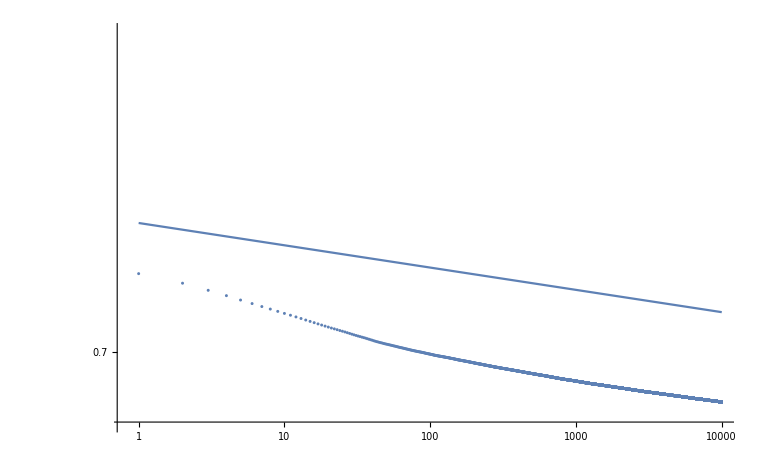

```mathematica
Show[
ListLogLogPlot[d2,PlotRange->{All,{0.65,0.975}}],
LogLogPlot[0.8*x^(-0.01),{x,1,10^4},PlotRange->{All,{0.65,0.975}}]
]
```

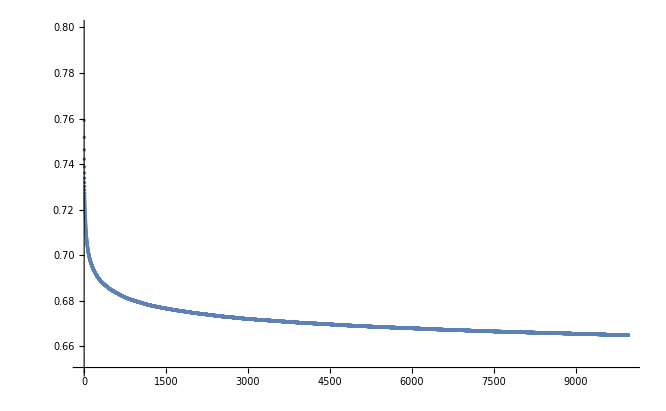

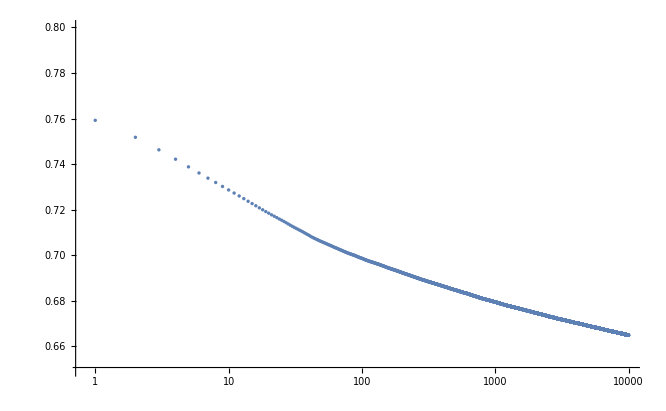

```mathematica
ListPlot[d2,PlotRange->{All,{0.65,0.8}}]
ListLogLinearPlot[d2,PlotRange->{All,{0.65,0.8}}]
```